```mathematica
dd[x_, k_, a_] := dd[x,k,a] = Sum[ dd[x/(j+a), k-1, a],{j,0,x-a}]
dd[x_, 0, a_] := 1
cc[x_, k_, a_] := a^(-k) dd[ x a^k, k, a+1]
```

```mathematica
dd[100,2,2]
```

283

```mathematica
cc[100,2,1.1]
```

281.818

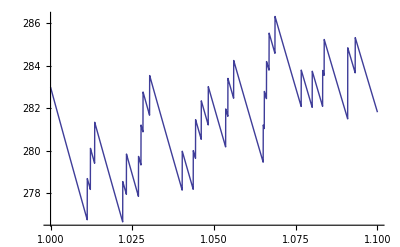

```mathematica
Plot[cc[100,2,n],{n,1,1.1}]
```